```mathematica
ClearAll["Global`*"]
```

```mathematica
Import["~/scf_arti_count.csv","Elements"]
```

{Data,Dataset,Dimensions,Grid,MaxColumnCount,RawData,RowCount,Summary}

```mathematica
scf= Import["~/scf_arti_count.csv"];
```

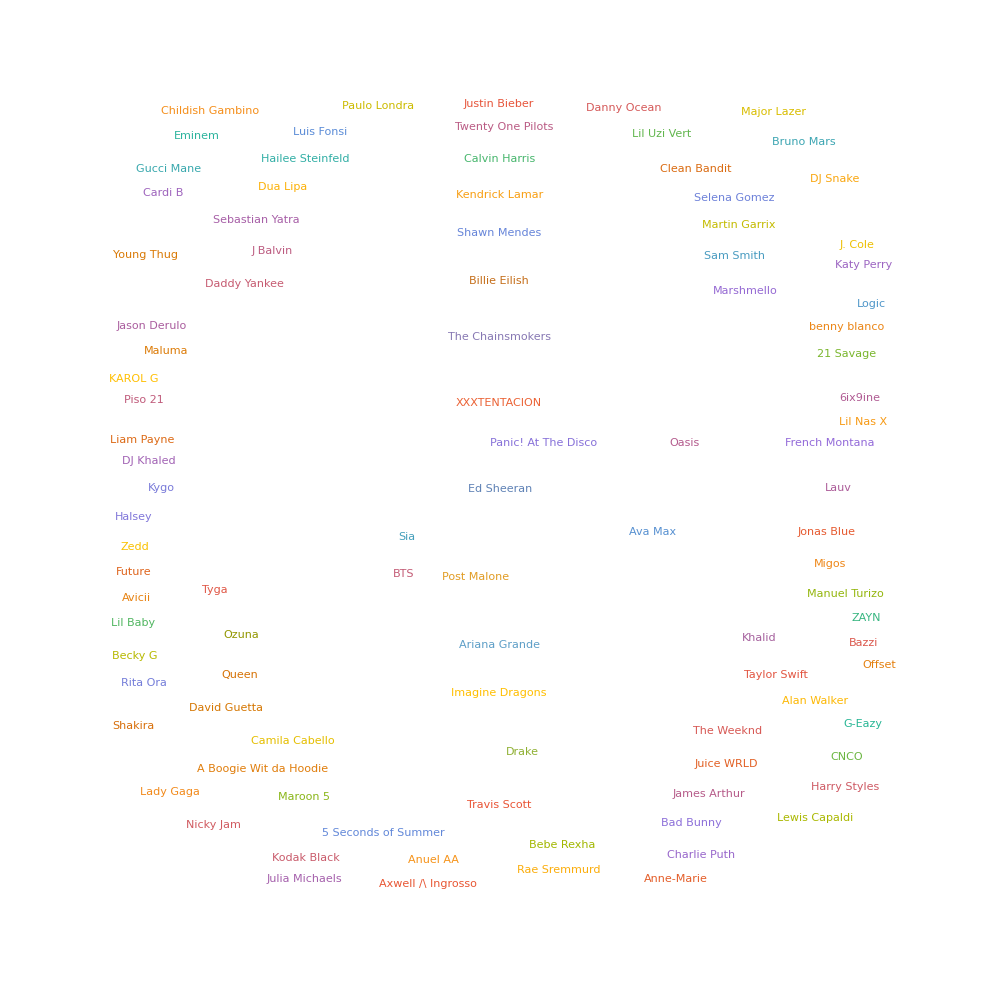

```mathematica
WordCloud[scf[[2;;-1,{2,4}]],ImageSize->1000]
```

```mathematica
Export["ArtistInfluence.png",WordCloud[scf[[2;;-1,{2,4}]],ImageSize->2000]]
```

ArtistInfluence.png